## Assignment 6

2.3.11(d,e)

(11) Evaluate the following generalized Fourier and inverse-Fourier integrals by hand:

(d) ∫_(-∞)^∞ t h(t) ⅇ^(ⅈ ω t)ⅆt , where h(t) is the Heaviside step function.

(e) ∫_0^∞ tanh(ω T)  sin ω t ⅆω/π (T>0).

### Solution

#### (d)

∫_0^∞ ⅆt  t ⅇ^(ⅈ ω t)=-ⅈ∂/(∂ω)∫_0^∞ ⅆt  ⅇ^(ⅈ ω t)=-ⅈ ∂/(∂ω)(-1/(ⅈ ω)+π δ(ω))=-1/ω^2-ⅈ π δ'(ω)

#### (e)

∫_0^∞ tanh(ω T)  sin ω t ⅆω/π=∫_0^∞ (tanh(ω T)-1)  sin ω t ⅆω/π+∫_0^∞ sin ω t ⅆω/π. The first integral can be done with Mathematica -- it is convergent.

```mathematica
Integrate[(Tanh[ω T]-1) Sin[ω t],{ω,0,Infinity},Assumptions->t ϵ Reals&&T>0]
```

ConditionalExpression[-1/t+(π Csch[(π t)/(2 T)])/(2 T),2 T>Abs[Im[t]]]

The second integral is a generalized Fourier integral. It can be done using a limiting procedure: lim_(⋁→ ∞) ∫_0^ν sin ω t ⅆω/π=lim_(⋁→ ∞) 1/(π t)(1-cos(ν t)). The second term oscillates infinitely rapidly (except at ω = 0 where it makes the integral finite). So we may write ∫_0^∞ sin ω t ⅆω/π=1/(π t), if t≠ 0,  throwing away the inifinitely rapid oscillation.  Adding the two results we get that the  integral equals Csch[(π t)/(2 T)]/(2 T)

2.3.19

(19) Use Fourier transform techniques to find and plot the current in amperes as a function of time in the circuit of Fig. 2.12 when the switch is closed at time t=0.

### Solution

The charge on the capcitors follows the ODE
L Q''+ R Q'+ Q/C = V(t). When the switch is closed, the voltage in the circuit behaves as V(t)= V h(t)where h(t) is a Heaviside step function. Fourier Transforming the equation to get a particular solution, we obtain
Q̃(ω) = V h̃(ω)/(-L ω^2-ⅈ R ω + 1/C). The Fourier transform of the step function is
h̃=π δ(ω)+ ⅈ/ω. Therefore the current is the inverse Fourier transform of -ⅈ ω Q̃:

```mathematica
Expand[-I ω V (Pi DiracDelta[ω] + I /ω)/(-L ω^2 -I ω R + 1/C)/.{L->25, C->15*^-6, R->2,V->1}]
```

1/(200000/3-2 ⅈ ω-25 ω^2)-(ⅈ π ω DiracDelta[ω])/(200000/3-2 ⅈ ω-25 ω^2)

```mathematica
current[t_] = InverseFourierTransform[%,ω,t]/Sqrt[2Pi]
```

-1/2 ⅈ √(3/4999997) ⅇ^(-1/75 (3+ⅈ √14999991) t) (-1+ⅇ^(2/25 ⅈ √(4999997/3) t)) HeavisideTheta[t]

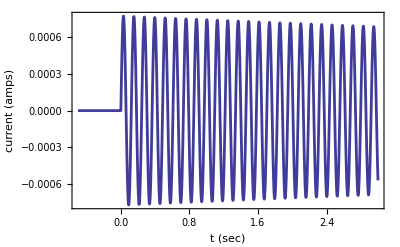

```mathematica
Plot[Re[current[t]],{t,-.5,3},PlotStyle->Thickness[0.005],Frame->True,FrameLabel->{"t (sec)","current (amps)"},Axes->False]
```

2.4.2(c,g)

(2) Use the method of Sec. 2.4.2 to solve the following ODEs for the Green's function, for the given homogeneous boundary or initial conditions:

(c) G'' +2 G'+G(t,t_o)=δ(t-t_o), G=0 for t<t_o. Plot G(t-t_o).

(g) G'' -κ_o^2 G(x,x_o)=δ(x-x_o),G=0 for x=a and x=b (κ_o real).

### Solutions

#### (c)

The general solution to the homogeneous problem is:

```mathematica
DSolve[x''[t] +2x'[t]+ x[t] ==0,x[t],t]
```

{{x[t]→ⅇ^-t C[1]+ⅇ^-t t C[2]}}

So we will construct a Greens function from two solutions, requiring that g=0 at t=t_0 and the derivative of g  with respect to t is 1 at t=t_0^+.

```mathematica
Clear["Global`*"]
```

```mathematica
g[t_] = c1 ⅇ^-t +c2 t ⅇ^-t;
```

```mathematica
Solve[{g[t0]==0,g'[t0]==1},{c1,c2}]
```

{{c1→-ⅇ^t0 t0,c2→ⅇ^t0}}

```mathematica
g[t_,t0_] = g[t]/.%[[1]]//Simplify
```

ⅇ^(-t+t0) (t-t0)

This is the solution for t>t_0

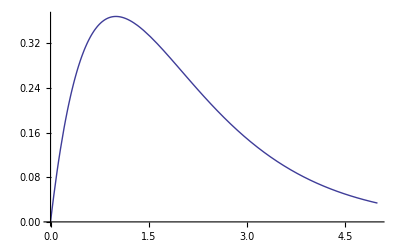

```mathematica
Plot[g[t,0],{t,0,5}]
```

#### (g)

The general solution to the homogeneous problem is:

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[ϕ''[x] -Subscript[κ, o]^2 ϕ[x] ==0,ϕ[x],x]
```

{{ϕ[x]→ⅇ^(-x κ_o) C[1]+ⅇ^(x κ_o) C[2]}}

So we will construct a Greens function from two solutions,

```mathematica
ϕ1[x_] = ⅇ^(-x Subscript[κ, o]);
ϕ2[x_] = ⅇ^(x Subscript[κ, o]);
```

We choose two linear combinations that vanish at x=a and x=b respectively:

```mathematica
ϕ1h[x_] = ⅇ^(-x Subscript[κ, o])-ⅇ^((x-2a) Subscript[κ, o]);
ϕ2h[x_] = ⅇ^(-x Subscript[κ, o])-ⅇ^((x-2b) Subscript[κ, o]);
```

The Wronskian is

```mathematica
W[x_] = FullSimplify[ϕ1h'[x] ϕ2h[x] - ϕ2h'[x] ϕ1h[x]]
```

2 (-ⅇ^(-2 a κ_o)+ⅇ^(-2 b κ_o)) κ_o

The Green's function is

```mathematica
g1[x_,x0_] = -ϕ2h[x0]ϕ1h[x]/W[x0]
```

((ⅇ^(-x κ_o)-ⅇ^((-2 a+x) κ_o)) (-ⅇ^(-x0 κ_o)+ⅇ^((-2 b+x0) κ_o)))/(2 (-ⅇ^(-2 a κ_o)+ⅇ^(-2 b κ_o)) κ_o)

This is the result for x<x_o. For x>x_o

```mathematica
g2[x_,x0_] = -ϕ1h[x0]ϕ2h[x]/W[x0]
```

((ⅇ^(-x κ_o)-ⅇ^((-2 b+x) κ_o)) (-ⅇ^(-x0 κ_o)+ⅇ^((-2 a+x0) κ_o)))/(2 (-ⅇ^(-2 a κ_o)+ⅇ^(-2 b κ_o)) κ_o)

```mathematica
g[x_,x0_] = Piecewise[{{ g1[x,x0] , x<x0}, {g2[x,x0], x≥ x0}}]
```

Piecewise[{{((ⅇ^(-x κ_o)-ⅇ^((-2 a+x) κ_o)) (-ⅇ^(-x0 κ_o)+ⅇ^((-2 b+x0) κ_o)))/(2 (-ⅇ^(-2 a κ_o)+ⅇ^(-2 b κ_o)) κ_o), x<x0}, {((ⅇ^(-x κ_o)-ⅇ^((-2 b+x) κ_o)) (-ⅇ^(-x0 κ_o)+ⅇ^((-2 a+x0) κ_o)))/(2 (-ⅇ^(-2 a κ_o)+ⅇ^(-2 b κ_o)) κ_o), x≥x0}, {0, True}}]

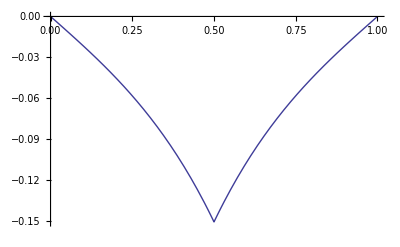

```mathematica
Plot[g[x,1/2]/.{Subscript[κ, o]->3, a->0,b->1},{x,0,1}]
```

2.4.3(c,g)

(3) Use the Green's functions found from Exercise (2) to help determine solutions to the following problems. Plot the solution in each case.

(c) x'' +2 x'+x(t)=t^2, x(0)=1,x'(0)=0.

(g) ϕ'' -ϕ(x)=sin x,ϕ'(0)=0 =ϕ(1).

### Solutions

#### (c)

From the previous problem the greens function is, for t>t0,

```mathematica
Clear["Global`*"]
```

```mathematica
g[t-t0]=ⅇ^(-t+t0) (t-t0)
```

ⅇ^(-t+t0) (t-t0)

So a particlar solution is

```mathematica
xp[t_] = Integrate[g[t-t0] t0^2,{t0,0,t}]
```

6+(-4+t) t-2 ⅇ^-t (3+t)

Add in a general homogeneous  solution:

```mathematica
xh[t_] = c1 Exp[-t] + c2 t Exp[-t];
```

```mathematica
x[t_]= xh[t] + xp[t];
```

Solve for the undetermined constants using the initial conditions:

```mathematica
Solve[{x[0]==1,x'[0]==0},{c1,c2}]
```

{{c1→1,c2→1}}

```mathematica
x[t_] = x[t]/.%[[1]]
```

6+ⅇ^-t+ⅇ^-t t+(-4+t) t-2 ⅇ^-t (3+t)

Check that this works

```mathematica
x''[t] + 2 x'[t] + x[t] == t^2 && x[0]==1&&x'[0]==0//Simplify
```

True

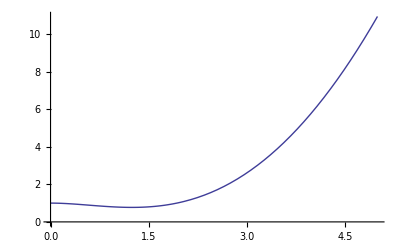

```mathematica
Plot[x[t],{t,0,5}]
```

#### (g)

```mathematica
Clear["Global`*"]
```

```mathematica
a=0;b=1;Subscript[κ, o]=1;
```

```mathematica
g[x_,x0_] =Piecewise[{{((ⅇ^(-x Subscript[κ, o])-ⅇ^((-2 a+x) Subscript[κ, o])) (-ⅇ^(-x0 Subscript[κ, o])+ⅇ^((-2 b+x0) Subscript[κ, o])))/(2 (-ⅇ^(-2 a Subscript[κ, o])+ⅇ^(-2 b Subscript[κ, o])) Subscript[κ, o]), x<x0}, {((ⅇ^(-x Subscript[κ, o])-ⅇ^((-2 b+x) Subscript[κ, o])) (-ⅇ^(-x0 Subscript[κ, o])+ⅇ^((-2 a+x0) Subscript[κ, o])))/(2 (-ⅇ^(-2 a Subscript[κ, o])+ⅇ^(-2 b Subscript[κ, o])) Subscript[κ, o]), x≥x0}, {0, True}}]
```

Piecewise[{{((ⅇ^-x-ⅇ^x) (ⅇ^(-2+x0)-ⅇ^-x0))/(2 (-1+1/ⅇ^2)), x<x0}, {((-ⅇ^(-2+x)+ⅇ^-x) (-ⅇ^-x0+ⅇ^x0))/(2 (-1+1/ⅇ^2)), x≥x0}, {0, True}}]

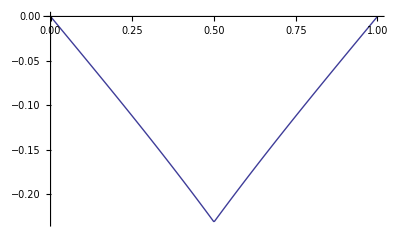

```mathematica
Plot[g[x,1/2],{x,0,1}]
```

Using Piecewise helps simplify the integrals in this problem. You don't have to break the integrand up.

```mathematica
ϕp[x_] = Integrate[g[x,x0]Sin[x0],{x0,a,b},Assumptions->a<x<b]//Simplify
```

(ⅇ^(1-x) (-1+ⅇ^(2 x)) Sin[1]-(-1+ⅇ^2) Sin[x])/(2 (-1+ⅇ^2))

Check

```mathematica
ϕp''[x] -ϕp[x] == Sin[x]//Simplify
```

True

Add in homogeneous solutions to match the boundary conditions

```mathematica
ϕh[x_] = c1 Exp[-x] + c2 Exp[x];
```

```mathematica
ϕ[x_] = ϕp[x] + ϕh[x];
```

```mathematica
Solve[{ϕ[1]==0,ϕ'[0]==0},{c1,c2}]
```

{{c1→-(ⅇ^2 (-1+ⅇ^2-2 ⅇ Sin[1]))/(2 (-1+ⅇ^4)),c2→-(1-ⅇ^2+2 ⅇ Sin[1])/(2 (-1+ⅇ^2) (1+ⅇ^2))}}

```mathematica
ϕ[x_] = ϕ[x]/.%[[1]]//Simplify
```

(ⅇ^-x (-ⅇ^2+ⅇ^(2 x)+ⅇ Sin[1]+ⅇ^(1+2 x) Sin[1]-ⅇ^x (1+ⅇ^2) Sin[x]))/(2 (1+ⅇ^2))

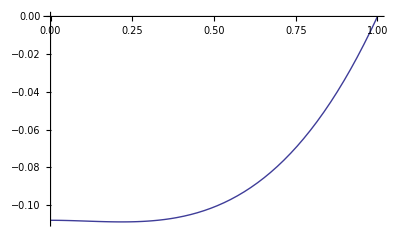

```mathematica
Plot[ϕ[x],{x,0,1}]
```